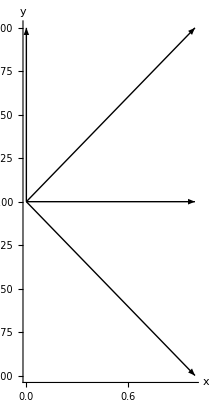

```mathematica
Graphics[{Arrow[{{0,0},{1,1}}],Arrow[{{0,0},{1,-1}}],Arrow[{{0,0},{1,0}}],Arrow[{{0,0},{0,1}}]},Axes->True,AxesLabel->{x,y}]
```

```mathematica
Manipulate[Plot3D[(2Abs[(Cos[Θ]+1)Cos[φ]Sin[θ]+Cos[θ]Cos[Φ]Sin[Θ]+Cos[Φ]Sin[Θ]])/(2p Sin[Θ]Sin[θ]Sin[Φ]Sin[φ]+2p Sin[Θ]Sin[θ] Cos[Φ]Cos[φ]-p Cos[θ](Cos[Θ]-1)+p Cos[Θ]+3),{Θ,0,Pi},{Φ,0,2Pi}],{θ,0,Pi},{φ,0,2Pi},{p,0,1}]
```

```mathematica
Manipulate[Plot3D[(2Abs[(Cos[Θ]+1)Cos[φ]Sin[θ]+Cos[θ]Cos[Φ]Sin[Θ]+Cos[Φ]Sin[Θ]])/(2p Sin[Θ]Sin[θ]Sin[Φ]Sin[φ]+2p Sin[Θ]Sin[θ] Cos[Φ]Cos[φ]-p Cos[θ](Cos[Θ]-1)+p Cos[Θ]+3),{θ,0,Pi},{φ,0,2Pi}],{Θ,0,Pi},{Φ,0,2Pi},{p,0,1}]
```

```mathematica
(2Abs[(Cos[Θ]+1)Cos[φ]Sin[θ]+Cos[θ]Cos[Φ]Sin[Θ]+Cos[Φ]Sin[Θ]])/(2p Sin[Θ]Sin[θ]Sin[Φ]Sin[φ]+2p Sin[Θ]Sin[θ] Cos[Φ]Cos[φ]-p Cos[θ](Cos[Θ]-1)+p Cos[Θ]+3)
```

(2 Abs[(1+Cos[Θ]) Cos[φ] Sin[θ]+Cos[Φ] Sin[Θ]+Cos[θ] Cos[Φ] Sin[Θ]])/(3-p Cos[θ] (-1+Cos[Θ])+p Cos[Θ]+2 p Cos[φ] Cos[Φ] Sin[θ] Sin[Θ]+2 p Sin[θ] Sin[Θ] Sin[φ] Sin[Φ])

```mathematica
Simplify[(2 Abs[(1+Cos[Θ]) Cos[φ] Sin[θ]+Cos[Φ] Sin[Θ]+Cos[θ] Cos[Φ] Sin[Θ]])/(3-p Cos[θ] (-1+Cos[Θ])+p Cos[Θ]+2 p Cos[φ] Cos[Φ] Sin[θ] Sin[Θ]+2 p Sin[θ] Sin[Θ] Sin[φ] Sin[Φ])]
```

```mathematica
(2 (1+Cos[Θ]) Cos[φ] Sin[θ]+(1+Cos[θ]) Cos[Φ] Sin[Θ])/(3+p Cos[Θ]+Cos[θ] (p-p Cos[Θ])+2 p Cos[φ] Cos[Φ] Sin[θ] Sin[Θ]+2 p Sin[θ] Sin[Θ] Sin[φ] Sin[Φ])
```

(2 (1+Cos[Θ]) Cos[φ] Sin[θ]+(1+Cos[θ]) Cos[Φ] Sin[Θ])/(3+p Cos[Θ]+Cos[θ] (p-p Cos[Θ])+2 p Cos[φ] Cos[Φ] Sin[θ] Sin[Θ]+2 p Sin[θ] Sin[Θ] Sin[φ] Sin[Φ])

```mathematica
Simplify[(2 (1+Cos[Θ]) Cos[φ] Sin[θ]+(1+Cos[θ]) Cos[Φ] Sin[Θ])/(3+p Cos[Θ]+Cos[θ] (p-p Cos[Θ])+2 p Cos[φ] Cos[Φ] Sin[θ] Sin[Θ]+2 p Sin[θ] Sin[Θ] Sin[φ] Sin[Φ])]
```

(2 (1+Cos[Θ]) Cos[φ] Sin[θ]+(1+Cos[θ]) Cos[Φ] Sin[Θ])/(3+p Cos[Θ]+Cos[θ] (p-p Cos[Θ])+2 p Cos[φ] Cos[Φ] Sin[θ] Sin[Θ]+2 p Sin[θ] Sin[Θ] Sin[φ] Sin[Φ])

```mathematica
Manipulate[SphericalPlot3D[(2 (1+Cos[Θ]) Cos[φ] Sin[θ]+(1+Cos[θ]) Cos[Φ] Sin[Θ])/(3+p Cos[Θ]+Cos[θ] (p-p Cos[Θ])+2 p Cos[φ] Cos[Φ] Sin[θ] Sin[Θ]+2 p Sin[θ] Sin[Θ] Sin[φ] Sin[Φ]),{θ,0,π},{φ,0,2 π}],{p,-1.9301898050140316,1.9301898050140316},{Θ,-0.5144755802991018,0.5144755802991018},{Φ,-2,2}]
```

```mathematica
1/3{{0,0,0,0,0,0,0,0},{0,1,1,0,1,0,0,0},{0,1,1,0,1,0,0,0},{0,0,0,0,0,0,0,0},{0,1,1,0,1,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}
```

{{0,0,0,0,0,0,0,0},{0,1/3,1/3,0,1/3,0,0,0},{0,1/3,1/3,0,1/3,0,0,0},{0,0,0,0,0,0,0,0},{0,1/3,1/3,0,1/3,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}

```mathematica
MatrixForm[{{0,0,0,0,0,0,0,0},{0,1/3,1/3,0,1/3,0,0,0},{0,1/3,1/3,0,1/3,0,0,0},{0,0,0,0,0,0,0,0},{0,1/3,1/3,0,1/3,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/3 | 1/3 | 0 | 1/3 | 0 | 0 | 0
0 | 1/3 | 1/3 | 0 | 1/3 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/3 | 1/3 | 0 | 1/3 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
TensorProduct[{1,0},{1,0},{0,1}]
```

{{{0,1},{0,0}},{{0,0},{0,0}}}

```mathematica
Flatten[{{{0,1},{0,0}},{{0,0},{0,0}}}]
```

{0,1,0,0,0,0,0,0}

```mathematica
1/(√3)(TensorProduct[{0,1},{1,0},{1,0}]+TensorProduct[{1,0},{1,0},{0,1}]+TensorProduct[{1,0},{0,1},{1,0}])
```

{{{0,1/(√3)},{1/(√3),0}},{{1/(√3),0},{0,0}}}

```mathematica
Flatten[{{{0,1/(√3)},{1/(√3),0}},{{1/(√3),0},{0,0}}}]
```

{0,1/(√3),1/(√3),0,1/(√3),0,0,0}

```mathematica
KroneckerProduct[{0,1/(√3),1/(√3),0,1/(√3),0,0,0},{0,1/(√3),1/(√3),0,1/(√3),0,0,0}]
```

{{0,0,0,0,0,0,0,0},{0,1/3,1/3,0,1/3,0,0,0},{0,1/3,1/3,0,1/3,0,0,0},{0,0,0,0,0,0,0,0},{0,1/3,1/3,0,1/3,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}

```mathematica
MatrixForm[{{0,0,0,0,0,0,0,0},{0,1/3,1/3,0,1/3,0,0,0},{0,1/3,1/3,0,1/3,0,0,0},{0,0,0,0,0,0,0,0},{0,1/3,1/3,0,1/3,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/3 | 1/3 | 0 | 1/3 | 0 | 0 | 0
0 | 1/3 | 1/3 | 0 | 1/3 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/3 | 1/3 | 0 | 1/3 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
TensorProduct[{{1,0},{0,0}},{{0.5,0},{0,0.5}},{{0.5,0},{0,0.5}}]
```

{{{{{{0.25,0.},{0.,0.25}},{{0.,0},{0,0.}}},{{{0.,0},{0,0.}},{{0.25,0.},{0.,0.25}}}},{{{{0.,0.},{0.,0.}},{{0.,0},{0,0.}}},{{{0.,0},{0,0.}},{{0.,0.},{0.,0.}}}}},{{{{{0.,0.},{0.,0.}},{{0.,0},{0,0.}}},{{{0.,0},{0,0.}},{{0.,0.},{0.,0.}}}},{{{{0.,0.},{0.,0.}},{{0.,0},{0,0.}}},{{{0.,0},{0,0.}},{{0.,0.},{0.,0.}}}}}}

```mathematica
Flatten[%13]
```

{0.25,0.,0.,0.25,0.,0,0,0.,0.,0,0,0.,0.25,0.,0.,0.25,0.,0.,0.,0.,0.,0,0,0.,0.,0,0,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0,0,0.,0.,0,0,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0,0,0.,0.,0,0,0.,0.,0.,0.,0.}

```mathematica
({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 1/24 (1-p) p, 0, 0, 0, 0, 0, 0}, {0, 0, 1/24 (1-p) p, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1/24 (1-p) p, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}}). 1/8({{Cos[x]+1, 0, 0, 0, Sin[x]Cos[y]-I Sin[x]Sin[y], 0, 0, 0}, {0, Cos[x]+1, 1/3, 0, 1/3, Sin[x]Cos[y]-I Sin[x]Sin[y], 0, 0}, {0, 1/3, Cos[x]+1, 0, 1/3, 0, Sin[x]Cos[y]-I Sin[x]Sin[y], 0}, {0, 0, 0, Cos[x]+1, 0, 0, 0, Sin[x]Cos[y]-I Sin[x]Sin[y]}, {Sin[x]Cos[y]+I Sin[x]Sin[y], 1/3, 1/3, 0, 1-Cos[x], 0, 0, 0}, {0, Sin[x]Cos[y]+I Sin[x]Sin[y], 0, 0, 0, 1-Cos[x], 0, 0}, {0, 0, Sin[x]Cos[y]+I Sin[x]Sin[y], 0, 0, 0, 1-Cos[x], 0}, {0, 0, 0, Sin[x]Cos[y]+I Sin[x]Sin[y], 0, 0, 0, 1-Cos[x]}})
```

{{0,0,0,0,0,0,0,0},{0,1/192 (1+1/(√2)) (1-p) p,1/576 (1-p) p,0,1/576 (1-p) p,(-1/384-ⅈ/384) (1-p) p,0,0},{0,1/576 (1-p) p,1/192 (1+1/(√2)) (1-p) p,0,1/576 (1-p) p,0,(-1/384-ⅈ/384) (1-p) p,0},{0,0,0,0,0,0,0,0},{(-1/384+ⅈ/384) (1-p) p,1/576 (1-p) p,1/576 (1-p) p,0,1/192 (1-1/(√2)) (1-p) p,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}

```mathematica
MatrixForm[%85]
```

```mathematica
Tr[({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 1/192 (1+1/(√2)) (1-p) p, 1/576 (1-p) p, 0, 1/576 (1-p) p, (-1/384-ⅈ/384) (1-p) p, 0, 0}, {0, 1/576 (1-p) p, 1/192 (1+1/(√2)) (1-p) p, 0, 1/576 (1-p) p, 0, (-1/384-ⅈ/384) (1-p) p, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {(-1/384+ⅈ/384) (1-p) p, 1/576 (1-p) p, 1/576 (1-p) p, 0, 1/192 (1-1/(√2)) (1-p) p, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}})]
```

1/192 (1-1/(√2)) (1-p) p+1/96 (1+1/(√2)) (1-p) p

```mathematica
Simplify[1/192 (1-1/(√2)) (1-p) p+1/96 (1+1/(√2)) (1-p) p]
```

-1/384 (6+√2) (-1+p) p

```mathematica
MatrixForm[%15]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/24 (Cos[y] Sin[x]+ⅈ Sin[x] Sin[y]) | 1/36+1/24 (1+Cos[x]) | 1/36+1/24 (1+Cos[x]) | 0 | 1/36+1/24 (1-Cos[x]) | 1/24 (Cos[y] Sin[x]-ⅈ Sin[x] Sin[y]) | 1/24 (Cos[y] Sin[x]-ⅈ Sin[x] Sin[y]) | 0
1/24 (Cos[y] Sin[x]+ⅈ Sin[x] Sin[y]) | 1/36+1/24 (1+Cos[x]) | 1/36+1/24 (1+Cos[x]) | 0 | 1/36+1/24 (1-Cos[x]) | 1/24 (Cos[y] Sin[x]-ⅈ Sin[x] Sin[y]) | 1/24 (Cos[y] Sin[x]-ⅈ Sin[x] Sin[y]) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/24 (Cos[y] Sin[x]+ⅈ Sin[x] Sin[y]) | 1/36+1/24 (1+Cos[x]) | 1/36+1/24 (1+Cos[x]) | 0 | 1/36+1/24 (1-Cos[x]) | 1/24 (Cos[y] Sin[x]-ⅈ Sin[x] Sin[y]) | 1/24 (Cos[y] Sin[x]-ⅈ Sin[x] Sin[y]) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
1/(√2)(TensorProduct[{0,1},{1,0}]+TensorProduct[{1,0},{0,1}])
```

{{0,1/(√2)},{1/(√2),0}}

```mathematica
Flatten[{{0,1/(√2)},{1/(√2),0}}]
```

{0,1/(√2),1/(√2),0}

```mathematica
KroneckerProduct[{0,1/(√2),1/(√2),0},{0,1/(√2),1/(√2),0}]
```

{{0,0,0,0},{0,1/2,1/2,0},{0,1/2,1/2,0},{0,0,0,0}}

```mathematica
MatrixForm[{{0,0,0,0},{0,1/2,1/2,0},{0,1/2,1/2,0},{0,0,0,0}}]
TensorProduct[{{Cos[θ]/2+1/2,0},{0,(-Cos[θ])/2+1/2}},{{1/2,0},{0,1/2}}]
```

(0 | 0 | 0 | 0
0 | 1/2 | 1/2 | 0
0 | 1/2 | 1/2 | 0
0 | 0 | 0 | 0)

{{{{1/2 (1/2+Cos[θ]/2),0},{0,1/2 (1/2+Cos[θ]/2)}},{{0,0},{0,0}}},{{{0,0},{0,0}},{{1/2 (1/2-Cos[θ]/2),0},{0,1/2 (1/2-Cos[θ]/2)}}}}

```mathematica
{{{{1/2 (1/2+Cos[θ]/2),0,0,1/2 (1/2+Cos[θ]/2)}},{{0,0,0,0}}},{{{0,0,0,0}},{{1/2 (1/2-Cos[θ]/2),0,0,1/2 (1/2-Cos[θ]/2)}}}}
```

{{{{1/2 (1/2+Cos[θ]/2),0,0,1/2 (1/2+Cos[θ]/2)}},{{0,0,0,0}}},{{{0,0,0,0}},{{1/2 (1/2-Cos[θ]/2),0,0,1/2 (1/2-Cos[θ]/2)}}}}

```mathematica
1/4({{Cos[θ]+1, 0, Sin[θ], 0}, {0, Cos[θ]+1, 0, Sin[θ]}, {Sin[θ], 0, 1-Cos[θ], 0}, {0, Sin[θ], 0, 1-Cos[θ]}})*({{0, 0, 0, 0}, {0, 1/2, 1/2, 0}, {0, 1/2, 1/2, 0}, {0, 0, 0, 0}})
```

{{0,0,0,0},{0,1/8 (1+Cos[θ]),0,0},{0,0,1/8 (1-Cos[θ]),0},{0,0,0,0}}

```mathematica
MatrixForm[{{0,0,0,0},{0,1/8 (1+Cos[θ]),0,0},{0,0,1/8 (1-Cos[θ]),0},{0,0,0,0}}]
```

(0 | 0 | 0 | 0
0 | 1/8 (1+Cos[θ]) | 0 | 0
0 | 0 | 1/8 (1-Cos[θ]) | 0
0 | 0 | 0 | 0)

```mathematica
({{0, 0, 0, 0}, {0, 1/8 (1+Cos[θ]), 0, 0}, {0, 0, 1/8 (1-Cos[θ]), 0}, {0, 0, 0, 0}})
```

```mathematica
{{1/8 (1-Cos[θ]),0},{0,1/8 (1+Cos[θ])}}
```

{{1/8 (1-Cos[θ]),0},{0,1/8 (1+Cos[θ])}}

```mathematica
MatrixForm[{{1/8 (1-Cos[θ]),0},{0,1/8 (1+Cos[θ])}}]
```

```mathematica
Tr[({{1/8 (1-Cos[θ]), 0}, {0, 1/8 (1+Cos[θ])}})]
```

1/8 (1-Cos[θ])+1/8 (1+Cos[θ])

```mathematica
Simplify[1/8 (1-Cos[θ])+1/8 (1+Cos[θ])]
```

1/4

```mathematica
({{(1+Cos[θ1]), Sin[θ1]}, {Sin[θ1], (1-Cos[θ1])}})*({{1/8 (1-Cos[θ]), 0}, {0, 1/8 (1+Cos[θ])}})
```

{{1/8 (1-Cos[θ]) (1+Cos[θ1]),0},{0,1/8 (1+Cos[θ]) (1-Cos[θ1])}}

```mathematica
MatrixForm[{{1/8 (1-Cos[θ]) (1+Cos[θ1]),0},{0,1/8 (1+Cos[θ]) (1-Cos[θ1])}}]
```

```mathematica
x=Pi/4
y=(3Pi)/4
```

π/4

(3 π)/4

```mathematica
Tr[({{1/8 (1-Cos[x]) (1+Cos[y]), 0}, {0, 1/8 (1+Cos[x]) (1-Cos[y])}})]
```

```mathematica
MatrixForm[({{1/8 (1-Cos[x]) (1+Cos[y]), 0}, {0, 1/8 (1+Cos[x]) (1-Cos[y])}})]
```

(1/8 (1-1/(√2)) (1+1/(√2)) | 0
0 | 1/8 (1-1/(√2)) (1+1/(√2)))

```mathematica
TensorProduct[{{1/2,0},{0,1/2}},{{1/2,0},{0,1/2}},{{(Cos[t]+1)/2,(Sin[t]Cos[T]-I Sin[t]Sin[T])/2},{(Sin[t]Cos[T]+I Sin[t]Sin[T])/2,(-Cos[t]+1)/2}}]
```

```mathematica
{{1/8 (1+Cos[t]),1/8 (Cos[T] Sin[t]-ⅈ Sin[t] Sin[T]),1/8 (Cos[T] Sin[t]+ⅈ Sin[t] Sin[T]),1/8 (1-Cos[t]),0,0,0,0},
{0,0,0,0,1/8 (1+Cos[t]),1/8 (Cos[T] Sin[t]-ⅈ Sin[t] Sin[T]),1/8 (Cos[T] Sin[t]+ⅈ Sin[t] Sin[T]),1/8 (1-Cos[t])},
{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},
{1/8 (1+Cos[t]),1/8 (Cos[T] Sin[t]-ⅈ Sin[t] Sin[T]),1/8 (Cos[T] Sin[t]+ⅈ Sin[t] Sin[T]),1/8 (1-Cos[t]),0,0,0,0},{0,0,0,0,1/8 (1+Cos[t]),1/8 (Cos[T] Sin[t]-ⅈ Sin[t] Sin[T]),1/8 (Cos[T] Sin[t]+ⅈ Sin[t] Sin[T]),1/8 (1-Cos[t])}}
```

{{1/8 (1+Cos[t]),1/8 (Cos[T] Sin[t]-ⅈ Sin[t] Sin[T]),1/8 (Cos[T] Sin[t]+ⅈ Sin[t] Sin[T]),1/8 (1-Cos[t]),0,0,0,0},{0,0,0,0,1/8 (1+Cos[t]),1/8 (Cos[T] Sin[t]-ⅈ Sin[t] Sin[T]),1/8 (Cos[T] Sin[t]+ⅈ Sin[t] Sin[T]),1/8 (1-Cos[t])},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{1/8 (1+Cos[t]),1/8 (Cos[T] Sin[t]-ⅈ Sin[t] Sin[T]),1/8 (Cos[T] Sin[t]+ⅈ Sin[t] Sin[T]),1/8 (1-Cos[t]),0,0,0,0},{0,0,0,0,1/8 (1+Cos[t]),1/8 (Cos[T] Sin[t]-ⅈ Sin[t] Sin[T]),1/8 (Cos[T] Sin[t]+ⅈ Sin[t] Sin[T]),1/8 (1-Cos[t])}}

```mathematica
MatrixForm[%66]
```

```mathematica
({{1/8 (1+Cos[t]), 1/8 (Cos[T] Sin[t]-ⅈ Sin[t] Sin[T]), 0, 0, 0, 0, 0, 0}, {1/8 (Cos[T] Sin[t]+ⅈ Sin[t] Sin[T]), 1/8 (1-Cos[t]), 0, 0, 0, 0, 0, 0}, {0, 0, 1/8 (1+Cos[t]), 1/8 (Cos[T] Sin[t]-ⅈ Sin[t] Sin[T]), 0, 0, 0, 0}, {0, 0, 1/8 (Cos[T] Sin[t]-ⅈ Sin[t] Sin[T]), 1/8 (1-Cos[t]), 0, 0, 0, 0}, {0, 0, 0, 0, 1/8 (1+Cos[t]), 1/8 (Cos[T] Sin[t]-ⅈ Sin[t] Sin[T]), 0, 0}, {0, 0, 0, 0, 1/8 (Cos[T] Sin[t]-ⅈ Sin[t] Sin[T]), 1/8 (1-Cos[t]), 0, 0}, {0, 0, 0, 0, 0, 0, 1/8 (1+Cos[t]), 1/8 (Cos[T] Sin[t]-ⅈ Sin[t] Sin[T])}, {0, 0, 0, 0, 0, 0, 1/8 (Cos[T] Sin[t]-ⅈ Sin[t] Sin[T]), 1/8 (1-Cos[t])}})
```

```mathematica
{{}{}{}{}{}{}{}{}}
```

```mathematica
p*({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 1/3, 1/3, 0, 1/3, 0, 0, 0}, {0, 1/3, 1/3, 0, 1/3, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 1/3, 1/3, 0, 1/3, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}})*((1-p)/8)({{1, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 1}})
```

{{0,0,0,0,0,0,0,0},{0,1/24 (1-p) p,0,0,0,0,0,0},{0,0,1/24 (1-p) p,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,1/24 (1-p) p,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}

```mathematica
MatrixForm[%81]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/24 (1-p) p | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1/24 (1-p) p | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1/24 (1-p) p | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
MatrixForm[%68]
```

```mathematica
({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 1/24 (1-p) p, 0, 0, 0, 0, 0, 0}, {0, 0, 1/24 (1-p) p, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1/24 (1-p) p, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}})*({{1/8 (1+Cos[t]), 1/8 (Cos[T] Sin[t]-ⅈ Sin[t] Sin[T]), 0, 0, 0, 0, 0, 0}, {1/8 (Cos[T] Sin[t]+ⅈ Sin[t] Sin[T]), 1/8 (1-Cos[t]), 0, 0, 0, 0, 0, 0}, {0, 0, 1/8 (1+Cos[t]), 1/8 (Cos[T] Sin[t]-ⅈ Sin[t] Sin[T]), 0, 0, 0, 0}, {0, 0, 1/8 (Cos[T] Sin[t]+ⅈ Sin[t] Sin[T]), 1/8 (1-Cos[t]), 0, 0, 0, 0}, {0, 0, 0, 0, 1/8 (1+Cos[t]), 1/8 (Cos[T] Sin[t]-ⅈ Sin[t] Sin[T]), 0, 0}, {0, 0, 0, 0, 1/8 (Cos[T] Sin[t]+ⅈ Sin[t] Sin[T]), 1/8 (1-Cos[t]), 0, 0}, {0, 0, 0, 0, 0, 0, 1/8 (1+Cos[t]), 1/8 (Cos[T] Sin[t]-ⅈ Sin[t] Sin[T])}, {0, 0, 0, 0, 0, 0, 1/8 (Cos[T] Sin[t]+ⅈ Sin[t] Sin[T]), 1/8 (1-Cos[t])}})
```

{{0,0,0,0,0,0,0,0},{0,1/192 (1-p) p (1-Cos[t]),0,0,0,0,0,0},{0,0,1/192 (1-p) p (1+Cos[t]),0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,1/192 (1-p) p (1+Cos[t]),0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}

```mathematica
MatrixForm[%83]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/192 (1-p) p (1-Cos[t]) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1/192 (1-p) p (1+Cos[t]) | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1/192 (1-p) p (1+Cos[t]) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
MatrixForm[%76]
```

```mathematica
Tr[({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 1/192 (1-p) p (1-Cos[t]), 0, 0, 0, 0, 0, 0}, {0, 0, 1/192 (1-p) p (1+Cos[t]), 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1/192 (1-p) p (1+Cos[t]), 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}})]
```

1/192 (1-p) p (1-Cos[t])+1/96 (1-p) p (1+Cos[t])

```mathematica
Simplify[1/192 (1-p) p (1-Cos[t])+1/96 (1-p) p (1+Cos[t])]
```

-1/192 (-1+p) p (3+Cos[t])

```mathematica
MatrixForm[%71]
```

```mathematica
Tr[({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 1/192 (1-p) p (1-Cos[t]), 0, 0, 0, 0, 0, 0}, {0, 0, 1/192 (1-p) p (1+Cos[t]), 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1/192 (1-p) p (1+Cos[t]), 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}})]
```

1/192 (1-p) p (1-Cos[t])+1/96 (1-p) p (1+Cos[t])

```mathematica
Simplify[1/192 (1-p) p (1-Cos[t])+1/96 (1-p) p (1+Cos[t])]
```

-1/192 (-1+p) p (3+Cos[t])

```mathematica
MatrixForm[{{0,0,0,0},{0,1,1,0},{0,1,1,0},{0,0,0,0}}]
```

```mathematica
Dot[1/4({{(1+Cos[t]), 0, (Cos[T] Sin[t]-ⅈ Sin[t] Sin[T]), 0}, {0, (1+Cos[t]), 1, (Cos[T] Sin[t]-ⅈ Sin[t] Sin[T])}, {(Cos[T] Sin[t]+ⅈ Sin[t] Sin[T]), 1, (1-Cos[t]), 0}, {0, (Cos[T] Sin[t]+ⅈ Sin[t] Sin[T]), 0, (1-Cos[t])}}),1/2({{0, 0, 0, 0}, {0, 1, 1, 0}, {0, 1, 1, 0}, {0, 0, 0, 0}})]
```

{{0,1/8 (Cos[T] Sin[t]-ⅈ Sin[t] Sin[T]),1/8 (Cos[T] Sin[t]-ⅈ Sin[t] Sin[T]),0},{0,1/8+1/8 (1+Cos[t]),1/8+1/8 (1+Cos[t]),0},{0,1/8+1/8 (1-Cos[t]),1/8+1/8 (1-Cos[t]),0},{0,1/8 (Cos[T] Sin[t]+ⅈ Sin[t] Sin[T]),1/8 (Cos[T] Sin[t]+ⅈ Sin[t] Sin[T]),0}}

```mathematica
MatrixForm[%249]
```

(0 | 1/8 (Cos[T] Sin[t]-ⅈ Sin[t] Sin[T]) | 1/8 (Cos[T] Sin[t]-ⅈ Sin[t] Sin[T]) | 0
0 | 1/8+1/8 (1+Cos[t]) | 1/8+1/8 (1+Cos[t]) | 0
0 | 1/8+1/8 (1-Cos[t]) | 1/8+1/8 (1-Cos[t]) | 0
0 | 1/8 (Cos[T] Sin[t]+ⅈ Sin[t] Sin[T]) | 1/8 (Cos[T] Sin[t]+ⅈ Sin[t] Sin[T]) | 0)

```mathematica
MatrixForm[%215]
```

(0 | 0 | 0 | 0
1/8 (Cos[T] Sin[t]+ⅈ Sin[t] Sin[T]) | 1/8+1/8 (1+Cos[t]) | 1/8+1/8 (1-Cos[t]) | 1/8 (Cos[T] Sin[t]-ⅈ Sin[t] Sin[T])
1/8 (Cos[T] Sin[t]+ⅈ Sin[t] Sin[T]) | 1/8+1/8 (1+Cos[t]) | 1/8+1/8 (1-Cos[t]) | 1/8 (Cos[T] Sin[t]-ⅈ Sin[t] Sin[T])
0 | 0 | 0 | 0)

```mathematica
Tr[({{0, 1/8 (Cos[T] Sin[t]-ⅈ Sin[t] Sin[T]), 1/8 (Cos[T] Sin[t]-ⅈ Sin[t] Sin[T]), 0}, {0, 1/8+1/8 (1+Cos[t]), 1/8+1/8 (1+Cos[t]), 0}, {0, 1/8+1/8 (1-Cos[t]), 1/8+1/8 (1-Cos[t]), 0}, {0, 1/8 (Cos[T] Sin[t]+ⅈ Sin[t] Sin[T]), 1/8 (Cos[T] Sin[t]+ⅈ Sin[t] Sin[T]), 0}})]
```

1/4+1/8 (1-Cos[t])+1/8 (1+Cos[t])

```mathematica
Simplify[1/4+1/8 (1-Cos[t])+1/8 (1+Cos[t])]
```

1/2

```mathematica
x=0
y=Pi
z=0
({{0, 1/8 (Cos[T] Sin[t]-ⅈ Sin[t] Sin[T]), 1/8 (Cos[T] Sin[t]-ⅈ Sin[t] Sin[T]), 0}, {0, 1/8+1/8 (1+Cos[t]), 1/8+1/8 (1+Cos[t]), 0}, {0, 1/8+1/8 (1-Cos[t]), 1/8+1/8 (1-Cos[t]), 0}, {0, 1/8 (Cos[T] Sin[t]+ⅈ Sin[t] Sin[T]), 1/8 (Cos[T] Sin[t]+ⅈ Sin[t] Sin[T]), 0}})
MatrixForm[2*{{1/8+1/8 (1-Cos[t]),1/8 (Cos[T] Sin[t]-ⅈ Sin[t] Sin[T])},{1/8 (Cos[T] Sin[t]+ⅈ Sin[t] Sin[T]),1/8+1/8 (1+Cos[t])}}]
```

0

π

0

{{0,1/8 (Cos[T] Sin[t]-ⅈ Sin[t] Sin[T]),1/8 (Cos[T] Sin[t]-ⅈ Sin[t] Sin[T]),0},{0,1/8+1/8 (1+Cos[t]),1/8+1/8 (1+Cos[t]),0},{0,1/8+1/8 (1-Cos[t]),1/8+1/8 (1-Cos[t]),0},{0,1/8 (Cos[T] Sin[t]+ⅈ Sin[t] Sin[T]),1/8 (Cos[T] Sin[t]+ⅈ Sin[t] Sin[T]),0}}

(2 (1/8+1/8 (1-Cos[t])) | 1/4 (Cos[T] Sin[t]-ⅈ Sin[t] Sin[T])
1/4 (Cos[T] Sin[t]+ⅈ Sin[t] Sin[T]) | 2 (1/8+1/8 (1+Cos[t])))

{{0,0,0,0},{1/8 (Cos[T] Sin[t]+ⅈ Sin[t] Sin[T]),1/8+1/8 (1+Cos[t]),1/8+1/8 (1-Cos[t]),1/8 (Cos[T] Sin[t]-ⅈ Sin[t] Sin[T])},{1/8 (Cos[T] Sin[t]+ⅈ Sin[t] Sin[T]),1/8+1/8 (1+Cos[t]),1/8+1/8 (1-Cos[t]),1/8 (Cos[T] Sin[t]-ⅈ Sin[t] Sin[T])},{0,0,0,0}}

(2 (1/8+1/8 (1-Cos[t])) | 1/4 (Cos[T] Sin[t]-ⅈ Sin[t] Sin[T])
1/4 (Cos[T] Sin[t]+ⅈ Sin[t] Sin[T]) | 2 (1/8+1/8 (1+Cos[t])))

```mathematica
MatrixForm[Dot[({{1/2 (1+Cos[Y]), (Cos[Z] Sin[Y]-ⅈ Sin[Y] Sin[Z])/2}, {(Cos[Z] Sin[Y]+ⅈ Sin[Y] Sin[Z])/2, 1/2 (1-Cos[Y])}}),({{2 (1/8+1/8 (1-Cos[X])), 1/4 (Cos[Z] Sin[X]-ⅈ Sin[X] Sin[Z])}, {1/4 (Cos[Z] Sin[X]+ⅈ Sin[X] Sin[Z]), 2 (1/8+1/8 (1+Cos[X]))}})]]
```

((1/8+1/8 (1-Cos[X])) (1+Cos[Y])+1/8 (Cos[Z] Sin[X]+ⅈ Sin[X] Sin[Z]) (Cos[Z] Sin[Y]-ⅈ Sin[Y] Sin[Z]) | 1/8 (1+Cos[Y]) (Cos[Z] Sin[X]-ⅈ Sin[X] Sin[Z])+(1/8+1/8 (1+Cos[X])) (Cos[Z] Sin[Y]-ⅈ Sin[Y] Sin[Z])
1/8 (1-Cos[Y]) (Cos[Z] Sin[X]+ⅈ Sin[X] Sin[Z])+(1/8+1/8 (1-Cos[X])) (Cos[Z] Sin[Y]+ⅈ Sin[Y] Sin[Z]) | (1/8+1/8 (1+Cos[X])) (1-Cos[Y])+1/8 (Cos[Z] Sin[X]-ⅈ Sin[X] Sin[Z]) (Cos[Z] Sin[Y]+ⅈ Sin[Y] Sin[Z]))

```mathematica
MatrixForm[%283]
```

((1/8+1/8 (1-Cos[X])) (1+Cos[Y])+1/8 (Cos[Z] Sin[X]+ⅈ Sin[X] Sin[Z]) (Cos[Z] Sin[Y]-ⅈ Sin[Y] Sin[Z]) | 1/8 (1+Cos[Y]) (Cos[Z] Sin[X]-ⅈ Sin[X] Sin[Z])+(1/8+1/8 (1+Cos[X])) (Cos[Z] Sin[Y]-ⅈ Sin[Y] Sin[Z])
1/8 (1-Cos[Y]) (Cos[Z] Sin[X]+ⅈ Sin[X] Sin[Z])+(1/8+1/8 (1-Cos[X])) (Cos[Z] Sin[Y]+ⅈ Sin[Y] Sin[Z]) | (1/8+1/8 (1+Cos[X])) (1-Cos[Y])+1/8 (Cos[Z] Sin[X]-ⅈ Sin[X] Sin[Z]) (Cos[Z] Sin[Y]+ⅈ Sin[Y] Sin[Z]))

```mathematica
MatrixForm[%213]
```

```mathematica
{{1/8 (1-Cos[t]),0},{0,1/8 (1+Cos[t])}}
```

{{1/8 (1-Cos[t]),0},{0,1/8 (1+Cos[t])}}

```mathematica
MatrixForm[{{1/8 (1-Cos[t]),0},{0,1/8 (1+Cos[t])}}]
```

```mathematica
({{1/2 (1-Cos[x]), 0}, {0, 1/2 (1+Cos[x])}})({{1/2 (1+Cos[x]), (Cos[y] Sin[x]-ⅈ Sin[x] Sin[y])/2}, {(Cos[y] Sin[x]-ⅈ Sin[x] Sin[y])/2, 1/2 (1-Cos[x])}})
```

{{1/4 (1-1/(√2)) (1+1/(√2)),0},{0,1/4 (1-1/(√2)) (1+1/(√2))}}

```mathematica
MatrixForm[{{1/4 (1-1/(√2)) (1+1/(√2)),0},{0,1/4 (1-1/(√2)) (1+1/(√2))}}]
```

π/4

0

0

```mathematica
RootReduce[Tr[({{1/2 (1+Cos[y]), (Cos[z] Sin[y]-ⅈ Sin[y] Sin[z])/2}, {(Cos[z] Sin[y]-ⅈ Sin[y] Sin[z])/2, 1/2 (1-Cos[y])}})({{1/2 (1-Cos[x]), 0}, {0, 1/2 (1+Cos[x])}})]]
```

1/4 (2-√2)

```mathematica
MatrixForm[({{1/2 (1+Cos[y]), (Cos[z] Sin[y]-ⅈ Sin[y] Sin[z])/2}, {(Cos[z] Sin[y]-ⅈ Sin[y] Sin[z])/2, 1/2 (1-Cos[y])}})({{1/2 (1-Cos[x]), 0}, {0, 1/2 (1+Cos[x])}})]
```

(1/2 (1-1/(√2)) | 0
0 | 0)

```mathematica
({{1/2 (1-Cos[x]), 0}, {0, 1/2 (1+Cos[x])}})({{1/2 (1+Cos[y]), (Cos[t] Sin[y]-ⅈ Sin[y] Sin[t])/2}, {(Cos[t] Sin[y]-ⅈ Sin[y] Sin[t])/2, 1/2 (1-Cos[y])}})
```

{{1/2 (1-1/(√2)),0},{0,0}}